```mathematica
SetDirectory[NotebookDirectory[]];
```

/Users/omar/Documents/GitHub/IntPointsFEM/mathematica_notebooks/Elementary_Contribution

## Analytical solution: linear case pag. 133 Coussy

```mathematica
matrule={μ->833.33333333333337,rw->0.1,p-> -40,σh->-50};
```

```mathematica
u={(p-σh)/(2μ)rw^2/r,0,0};
Gradu=Grad[u,{r,θ,z},"Cylindrical"];
ϵ=1/2(Gradu+Transpose[Gradu])
σ=2μ  ϵ + λ Tr[ϵ] IdentityMatrix[3]
Div[σ,{r,θ,z},"Cylindrical"]=={0,0,0}
```

{{-(rw^2 (p-σh))/(2 r^2 μ),0,0},{0,(rw^2 (p-σh))/(2 r^2 μ),0},{0,0,0}}

{{-(rw^2 (p-σh))/r^2,0,0},{0,(rw^2 (p-σh))/r^2,0},{0,0,0}}

True

```mathematica
ϵ//.matrule
σ//.matrule
```

{{-0.00006/r^2,0,0},{0,0.00006/r^2,0},{0,0,0}}

{{-0.1/r^2,0,0},{0,0.1/r^2,0},{0,0,0}}

## Energy norm data for p={1,2,3}

```mathematica
hbase=0.00712436;
hdata={hbase,hbase/2,hbase/4,hbase/8};
```

```mathematica
ep1={1.63681295278*10^-6,4.35475260243*10^-7,1.0520553163*10^-7,2.534236049109*10^-8};
ep2={3.76932130202*10^-9,2.41937491203*10^-10,1.540674776*10^-11,9.3724117645*10^-13};
ep1=√ep1;
ep2=√ep2;
```

## Plot data

Plot Details

```mathematica
miniature=Import["drilling_vertical_borehole.png"];
```

```mathematica
fonts=16;
labelfonts=16;
```

```mathematica
datap1=Table[{hdata[[i]],ep1[[i]]},{i,1,4}];
datap2=Table[{hdata[[i]],ep2[[i]]},{i,1,4}];
```

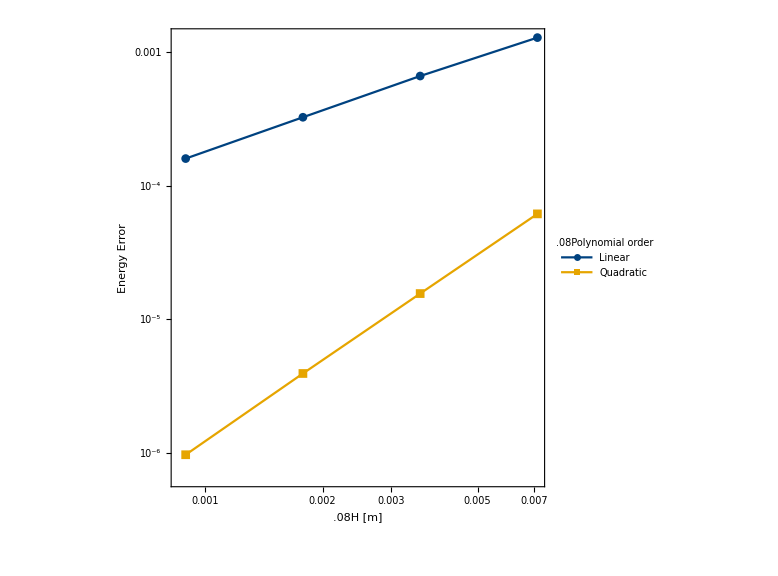

```mathematica
gErrorPlot=ListLogLogPlot[{datap1,datap2},Joined->True,PlotMarkers->Automatic,AspectRatio->1,PlotLegends->Placed[LineLegend[{Style["Linear",Black,fonts],Style["Quadratic",Black,fonts]},LegendLabel->Style[".08Polynomial order",Black,fonts],LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],{0.8,0.2}],Frame->True,FrameStyle->Directive[Black,FontSize->labelfonts],GridLines->Automatic,PlotStyle->ColorData[81,"ColorList"],ImageSize->Large,FrameLabel->{Style[".08H [m] ",Black,fonts],Style["Energy Error",Black,fonts]}]
```

## Exporting graphics

```mathematica
ExportQ = False;
```

```mathematica
If[ExportQ,
Export["approximation_rates.png",gErrorPlot,ImageResolution-> 100];
];
```